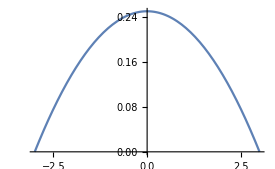

```mathematica
S[r_]=(-r^2+rc^2)((64 rc^9)/27)^(-1/3);
Plot[S[r]/.rc->3,{r,-3,3}]
```

```mathematica
(3/4)^(1/3)1/rc^3
```

```mathematica
Integrate[S[rx]S[ry]S[rz],{rx,-rc,rc},{ry,-rc,rc},{rz,-rc,rc}]
```

1

```mathematica
r1abs=(x1^2+y1^2+z1^2)^(1/2);
r2abs=(x2^2+y2^2+z2^2)^(1/2);
r1vec={x1,y1,z1};
r2vec={x2,y2,z2};
rij={sep,0,0};
diff=r2vec-rij
diffabs=(diff[[1]]^2+diff[[2]]^2+diff[[3]]^2)^(1/2)
rad=r2vec-r1vec
radabs=(rad[[1]]^2+rad[[2]]^2+rad[[3]]^2)^(1/2)
```

{-sep+x2,y2,z2}

√((-sep+x2)^2+y2^2+z2^2)

{-x1+x2,-y1+y2,-z1+z2}

√((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)

```mathematica
S[r1abs]S[diffabs]((r2vec-r1vec)/radabs^3)[[1]]
```

(9 (-x1+x2) (rc-√(x1^2+y1^2+z1^2)) (rc-√((-sep+x2)^2+y2^2+z2^2)))/(π^2 rc^2 ((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)^(3/2))

```mathematica
reprules={x1->(ρ1 Sin[θ1]Cos[ϕ1]),y1->(ρ1 Sin[θ1]Sin[ϕ1]),z1->(ρ1 Cos[θ1]),x2->(ρ2 Sin[θ2]Cos[ϕ2])+sep,y2->(ρ2 Sin[θ2]Sin[ϕ2]),z2->(ρ2 Cos[θ2])}
```

{x1→ρ1 Cos[ϕ1] Sin[θ1],y1→ρ1 Sin[θ1] Sin[ϕ1],z1→ρ1 Cos[θ1],x2→sep+ρ2 Cos[ϕ2] Sin[θ2],y2→ρ2 Sin[θ2] Sin[ϕ2],z2→ρ2 Cos[θ2]}

```mathematica
FullSimplify[(9 (-x1+x2) (rc-√(x1^2+y1^2+z1^2)) (rc-√((sep-x2)^2+y2^2+z2^2)))/(π^2 rc^2 ((x1-x2)^2+(y1-y2)^2+(z1-z2)^2)^(3/2))ρ1^2 Sin[θ1] ρ2^2 Sin[θ2]/.reprules,Assumptions->{rc>0,sep>0,ρ1>0,ρ2>0}]
```

(9 ρ1^2 (-rc+ρ1) ρ2^2 (-rc+ρ2) Sin[θ1] Sin[θ2] (sep-ρ1 Cos[ϕ1] Sin[θ1]+ρ2 Cos[ϕ2] Sin[θ2]))/(π^2 rc^2 ((ρ1 Cos[θ1]-ρ2 Cos[θ2])^2+(sep-ρ1 Cos[ϕ1] Sin[θ1]+ρ2 Cos[ϕ2] Sin[θ2])^2+(ρ1 Sin[θ1] Sin[ϕ1]-ρ2 Sin[θ2] Sin[ϕ2])^2)^(3/2))

```mathematica
Integrate[(9 ρ1^2 (-rc+ρ1) ρ2^2 (-rc+ρ2) Sin[θ1] Sin[θ2] (sep-ρ1 Cos[ϕ1] Sin[θ1]+ρ2 Cos[ϕ2] Sin[θ2]))/(π^2 rc^2 ((ρ1 Cos[θ1]-ρ2 Cos[θ2])^2+(sep-ρ1 Cos[ϕ1] Sin[θ1]+ρ2 Cos[ϕ2] Sin[θ2])^2+(ρ1 Sin[θ1] Sin[ϕ1]-ρ2 Sin[θ2] Sin[ϕ2])^2)^(3/2)),{ρ1,0,rc},{ρ2,0,rc},Assumptions->{rc>0,sep>0}]
```

$Aborted

```mathematica
NIntegrate[1/(π^2 rc^2)(9 ρ1^2 (-rc+ρ1) ρ2^2 (-rc+ρ2) Sin[θ1] Sin[θ2] (sep-ρ1 Cos[ϕ1] Sin[θ1]+ρ2 Cos[ϕ2] Sin[θ2]))/(((ρ1 Cos[θ1]-ρ2 Cos[θ2])^2+(sep-ρ1 Cos[ϕ1] Sin[θ1]+ρ2 Cos[ϕ2] Sin[θ2])^2+(ρ1 Sin[θ1] Sin[ϕ1]-ρ2 Sin[θ2] Sin[ϕ2])^2)^(3/2))/.rc->1/.sep->0.9,{ρ1,0,1},{ρ2,0, 1},{θ1,0,π},{θ2,0, π},{ϕ1,0,2π},{ϕ2,0,2π}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 0.777887 and 0.204685 for the integral and error estimates.

0.777887

```mathematica
1.0/0.5^2
```

4.

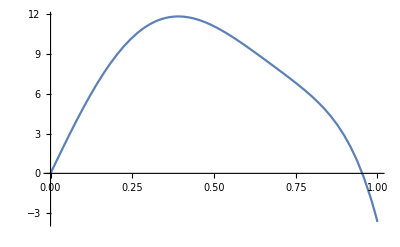

```mathematica
Plot[4/(35 rc)(224 ζ -224 ζ^3+70 ζ^4+48 ζ^5-21 ζ^6)/.ζ->(2 r)/rc/.r->x rc/.rc->1,{x,0,1}]
```

```mathematica
4/(35 rc)(224 ζ -224 ζ^3+70 ζ^4+48 ζ^5-21 ζ^6)/.ζ->(2 r)/rc/.r->x rc/.rc->1
```

4/35 (448 x-1792 x^3+1120 x^4+1536 x^5-1344 x^6)

```mathematica
S[x1]S[y1]S[z1]S[diff[[1]]]S[diff[[2]]]S[diff[[3]]]((r2vec-r1vec)/radabs^3)[[1]]
```

(729 (rc^2-x1^2) (-x1+x2) (rc^2-(-sep+x2)^2) (rc^2-y1^2) (rc^2-y2^2) (rc^2-z1^2) (rc^2-z2^2))/(4096 rc^18 ((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)^(3/2))

```mathematica
NIntegrate[(729 (rc^2-x1^2) (-x1+x2) (rc^2-(-sep+x2)^2) (rc^2-y1^2) (rc^2-y2^2) (rc^2-z1^2) (rc^2-z2^2))/(4096 rc^18 ((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)^(3/2))/.rc->1/.sep->1.5,{x1,-1,1},{x2,1.5-1,1.5+1},{y1,-1,1},{y2,-1,1},{z1,-1,1},{z2,-1,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 12087.1 and 108015. for the integral and error estimates.

12087.1

```mathematica
1.0/3^2
```

0.111111

```mathematica
Integrate[S[x]/.rc->1,{x,0,1}]//N
```

0.477465

```mathematica
NIntegrate[S[x1]S[y1]S[z1]S[diff[[1]]]S[diff[[2]]]S[diff[[3]]]/.rc->1/.sep->3,{x1,-1,1},{y1,-1,1},{z1,-1,1},{x2,3-1,3+1},{y2,-1,1},{z2,-1,1}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 1. and 0.000623301 for the integral and error estimates.

1.

```mathematica
S[diff[[1]]]S[diff[[2]]]S[diff[[3]]]
```

(27 (rc^2-(-sep+x2)^2) (rc^2-y2^2) (rc^2-z2^2))/(64 rc^9)

```mathematica
Integrate[(729 (rc^2-x1^2) (-x1+x2) (rc^2-(-sep+x2)^2) (rc^2-y1^2) (rc^2-y2^2) (rc^2-z1^2) (rc^2-z2^2))/(4096 rc^18 ((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)^(3/2)),{x1,-rc,rc},{x2,sep-rc,sep+rc},{y1,-rc,rc},{y2,-rc,rc},{z1,-rc,rc},{z2,-rc,rc},Assumptions->{sep>2rc,rc>0}]
```

$Aborted

```mathematica
Integrate[(729 (rc^2-x1^2) (-x1+x2) (rc^2-(-sep+x2)^2) (rc^2-y1^2) (rc^2-y2^2) (rc^2-z1^2) (rc^2-z2^2))/(4096 rc^18 ((-x1+x2)^2+(-y1+y2)^2+(-z1+z2)^2)^(3/2)),{x1,-rc,rc},{x2,sep-rc,sep+rc},{y1,-rc,rc},{y2,-rc,rc},{z1,-rc,rc},{z2,-rc,rc},Assumptions->{sep>2rc,rc>0}]
```